```mathematica
ConstantArray[0,300]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
fma[x_,y_,z_]:=x*y+z
```

```mathematica
ConstantArray[IntegerPart[fma[100,0.5,-0.5]*100]
```

4950

```mathematica
PadLeft[{1,2,3,4},8]
```

{0,0,0,0,1,2,3,4}

```mathematica
PadLeft[IntegerDigits[10,2],7]
```

{0,0,0,1,0,1,0}

```mathematica
FromDigits[IntegerDigits[10011011],2]
```

155

```mathematica
IntegerDigits[000100110110011100000010001101000110000000100101011001110000000100100100010101110000001101100111000000010101011001110000000100100110011100000001010101100000000100110100000000010010010000000010001101010000001101000101000000010011010101100000000101000101000000100011011000000010010001010000001101000000000101000110000000100100011001110000]
```

```mathematica
Partition[{0,0,0,1,0,0,1,1,0,1,1,0,0,1,1,1,0,0,0,0,0,0,1,0,0,0,1,1,0,1,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,1,0,1,0,1,1,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,1,0,1,0,1,1,1,0,0,0,0,0,0,1,1,0,1,1,0,0,1,1,1,0,0,0,0,0,0,0,1,0,1,0,1,0,1,1,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,1,1,1,0,0,0,0,0,0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,1,0,1,0,0,0,0,0,0,1,1,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,1,0,0,1,1,1,0,0,0,0},4]
```

```mathematica
Map[FromDigits[#,2]&,{{0,0,0,1},{0,0,1,1},{0,1,1,0},{0,1,1,1},{0,0,0,0},{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,1,1,0},{0,0,0,0},{0,0,1,0},{0,1,0,1},{0,1,1,0},{0,1,1,1},{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0},{0,1,0,1},{0,1,1,1},{0,0,0,0},{0,0,1,1},{0,1,1,0},{0,1,1,1},{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,1,1,0},{0,1,1,1},{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,1,0},{0,1,1,1},{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,1,1,0},{0,0,0,0},{0,0,0,1},{0,0,1,1},{0,1,0,0},{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0},{0,0,0,0},{0,0,1,0},{0,0,1,1},{0,1,0,1},{0,0,0,0},{0,0,1,1},{0,1,0,0},{0,1,0,1},{0,0,0,0},{0,0,0,1},{0,0,1,1},{0,1,0,1},{0,1,1,0},{0,0,0,0},{0,0,0,1},{0,1,0,0},{0,1,0,1},{0,0,0,0},{0,0,1,0},{0,0,1,1},{0,1,1,0},{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,1,0,1},{0,0,0,0},{0,0,1,1},{0,1,0,0},{0,0,0,0},{0,0,0,1},{0,1,0,0},{0,1,1,0},{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,1,1,0},{0,1,1,1},{0,0,0,0}}]
```

{1,3,6,7,0,2,3,4,6,0,2,5,6,7,0,1,2,4,5,7,0,3,6,7,0,1,5,6,7,0,1,2,6,7,0,1,5,6,0,1,3,4,0,1,2,4,0,2,3,5,0,3,4,5,0,1,3,5,6,0,1,4,5,0,2,3,6,0,2,4,5,0,3,4,0,1,4,6,0,2,4,6,7,0}

```mathematica
diff[list_]:=Block[{avgval=Mean[Map[Mean,list]],avglen=Mean[Map[Length,list]],maxval=Max[Flatten[list]]},
{((Ceiling[Log10[avgval]]+1)*avglen+1)*8,(Ceiling[Log2[maxval]]*avglen+1)*2^Ceiling[Log2[maxval]]}]
```

```mathematica
diflist=Monitor[Table[diff[Block[{r=RandomInteger[{1,100}]},
Map[RandomInteger[{1,r},#]&,RandomInteger[{1,100},RandomInteger[{1,100}]]]]],{i,1,100000}],i];
```

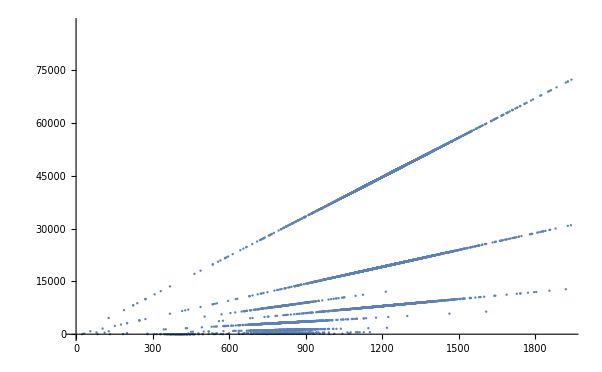

```mathematica
ListPlot[%]
```

```mathematica
data=diflist;
line = Fit[data, {1,x},x]
parabola = Fit[data, {1,x,x^2}, x]
```

-24664.8+42.6098 x

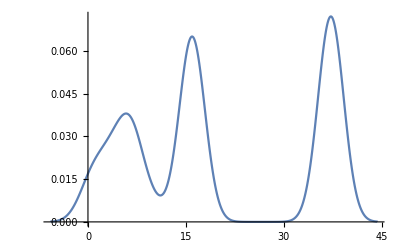

```mathematica
SmoothHistogram[Map[#[[2]]/#[[1]]&,diflist]]
```